```mathematica
Needs["ErrorBarPlots`"]
```

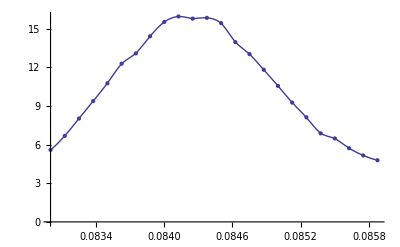

```mathematica
(*for l=30 & 40*)
v=9;
l=8;
vv=ToString[v];
ll=ToString[l];
Chi1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-1.txt",{Number,Number}];
Chit1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-1.txt",{Number,Number}];
Chi2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-2.txt",{Number,Number}];
Chit2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-2.txt",{Number,Number}];
Chi3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-3.txt",{Number,Number}];
Chit3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-3.txt",{Number,Number}];
Chi4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-4.txt",{Number,Number}];
Chit4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-4.txt",{Number,Number}];

Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]])/4.},{i,1,Length[Chi1]}];


(*Chi5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-5.txt",{Number,Number}];
Chit5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-5.txt",{Number,Number}];
Chi6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-6.txt",{Number,Number}];
Chit6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-6.txt",{Number,Number}];
Chi7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-7.txt",{Number,Number}];
Chit7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-7.txt",{Number,Number}];
Chi8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-8.txt",{Number,Number}];
Chit8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-8.txt",{Number,Number}];


Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]])/8.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]]+Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]])/8.},{i,1,Length[Chi1]}];*)

(*for l=30 & 40*)
(*Chi9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-9.txt",{Number,Number}];
Chit9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-9.txt",{Number,Number}];
Chi10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-10.txt",{Number,Number}];
Chit10=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-10.txt",{Number,Number}];
Chi11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-11.txt",{Number,Number}];
Chit11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-11.txt",{Number,Number}];
Chi12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-12.txt",{Number,Number}];
Chit12=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-12.txt",{Number,Number}];

Chi[v][l]=Table[{Chi1[[All,1]][[i]],(Chi1[[All,2]][[i]]+Chi2[[All,2]][[i]]+Chi3[[All,2]][[i]]+Chi4[[All,2]][[i]]+Chi5[[All,2]][[i]]+Chi6[[All,2]][[i]]+Chi7[[All,2]][[i]]+Chi8[[All,2]][[i]]+Chi9[[All,2]][[i]]+Chi10[[All,2]][[i]]+Chi11[[All,2]][[i]]+Chi12[[All,2]][[i]])/12.},{i,1,Length[Chi1]}];
Chit[v][l]=Table[{Chit1[[All,1]][[i]],(Chit1[[All,2]][[i]]+Chit2[[All,2]][[i]]+Chit3[[All,2]][[i]]+Chit4[[All,2]][[i]]+Chit5[[All,2]][[i]]+Chit6[[All,2]][[i]]+Chit7[[All,2]][[i]]+Chit8[[All,2]][[i]]+Chit9[[All,2]][[i]]+Chit10[[All,2]][[i]]+Chit11[[All,2]][[i]]+Chit12[[All,2]][[i]])/12.},{i,1,Length[Chi1]}];*)




Cht4[v][l]=Chit[v][l];
Ch4[v][l]=Chi[v][l];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

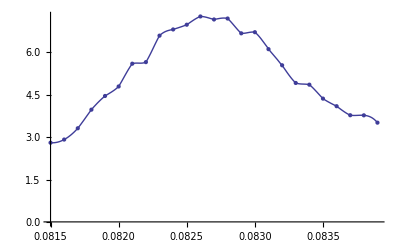

```mathematica
150, 200,4, 8:4
30, 40 :12
16,100:8
50,20,10:10
5: 2*5
```

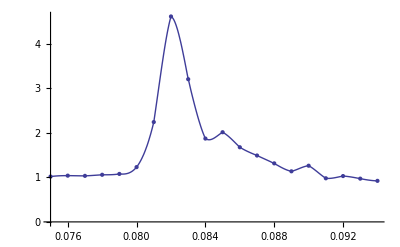

```mathematica
v=9;
l=100;
Cht4[v][l]=Chit[v][l];
Ch4[v][l]=Chi[v][l];

i4[v][l]=Interpolation[Ch4[v][l]];
it4[v][l]=Interpolation[Cht4[v][l]];

pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
Maxx={};
Maxy={};
Do[
Do[
Maxd[v][l]=Sort[Ch4[v][l],#1[[2]]>#2[[2]]&];
Maxx=Append[Maxx,{l*1000,Maxd[v][l][[All,1]][[1]]}];
Maxy=Append[Maxy,{l*1000,Maxd[v][l][[All,2]][[1]]}];
,{v,{9}}]
,{l,{4,5,8,10,16,20,30,40,50,100,150,200}}]
```

```mathematica
Maxx={{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}
Maxy={{4000,21.65885},{5000,19.60315},{8000,15.959175},{10000,14.64014},{16000,11.476725},{20000,9.729393000000002},{30000,7.3744375},{40000,6.557308333333333},{50000,6.02102},{100000,4.6185275},{150000,2.5028900000000003},{200000,2.4837325}}
```

{{4000,0.0855},{5000,0.085},{8000,0.084125},{10000,0.0838},{16000,0.08325},{20000,0.083},{30000,0.0827},{40000,0.0826},{50000,0.0821},{100000,0.082},{150000,0.0817},{200000,0.0817}}

{{4000,21.6589},{5000,19.6032},{8000,15.9592},{10000,14.6401},{16000,11.4767},{20000,9.72939},{30000,7.37444},{40000,6.55731},{50000,6.02102},{100000,4.61853},{150000,2.50289},{200000,2.48373}}

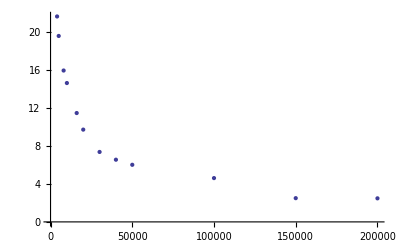

-Graphics-

```mathematica
ListPlot[Maxy]
ListPlot[Maxy]
```

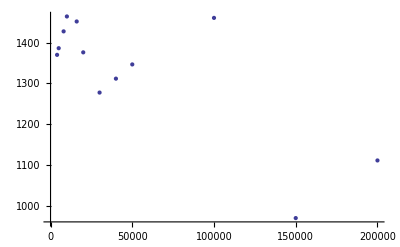

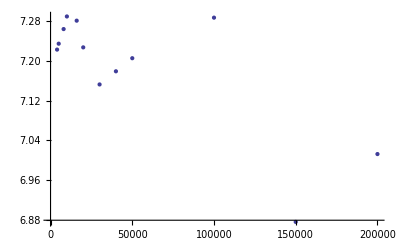

```mathematica
α=0.5;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]*Maxy[[All,1]][[i]]^α},{i,1,Length[Maxy]}];
Maxysl=Table[{Maxy[[All,1]][[i]],Log[Maxy[[All,2]][[i]]]+Log[Maxy[[All,1]][[i]]]*α},{i,1,Length[Maxy]}];
ListPlot[Maxys]
ListPlot[Maxysl]
```

fit :  (0.0812201+0.374587/x^0.54)

0.997587 = r0

0.54 = z0

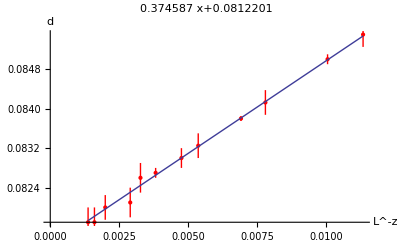

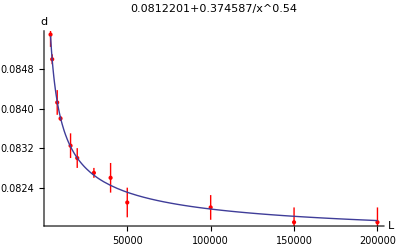

{0.0812201+0.374587/x^0.54, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0812201 | 0.000040313 | 2014.74 | 2.23312×10^-29
1/x^0.54 | 0.374587 | 0.0058264 | 64.2914 | 2.01725×10^-14}

FittedModel[-0.822931-0.557071 x]

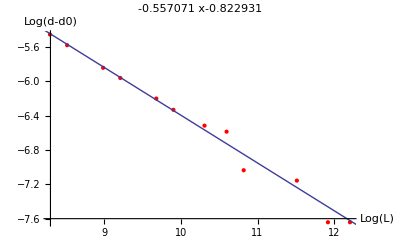

{-0.822931-0.557071 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.822931 | 0.170458 | -4.82776 | 0.000694109
x | -0.557071 | 0.0177209 | -31.4358 | 2.4935×10^-11}

```mathematica
ClearAll[z,r,x,k]
r0=0;
For[z=0.0,z<1.5,z+=0.01;
Maxxs=Table[{Maxx[[All,1]][[i]],Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
model=k*x^-z+d;
fit=LinearModelFit[Maxxs,{1,x^-z},x,Weights->1/Errorx^2];
(*fit=NonlinearModelFit[Maxxs,model,{k,d},x,Weights->1/Errorx^2];*)

r=fit["RSquared"];
r
If[r>r0,
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
r0=r;
z0=z;
]


]
ffit "fit : "
r0 "= r0"
z0 "= z0"
Maxxs=Table[{Maxx[[All,1]][[i]]^-z0,Maxx[[All,2]][[i]]},{i,1,Length[Maxx]}];
errx=Table[Errorx[[i]]*(z0)*Maxx[[All,1]][[i]]^(-z0-1),{i,1,Length[Errorx]}];
maxxerrs=Table[{Maxxs[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxxerrs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->val[[1]][[1]]+val[[2]][[1]]*"x"];
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxx[[All,1]][[1]]^-z0,Maxx[[All,1]][[Length[Maxx]]]^-z0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
pic1=ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-z0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]

ClearAll[k,x,z]
Maxxzcheck=Table[{Log[Maxx[[All,1]][[i]]],Log[Maxx[[All,2]][[i]]-val[[1]][[1]]]},{i,1,Length[Maxx]}];
Errorxzcheck=Table[Errorx[[i]]/Maxxzcheck[[All,2]][[i]],{i,1,Length[Maxx]}];
model=k-z*x;
fit=LinearModelFit[Maxxzcheck,{1,x},x,Weights->1/Errorxzcheck^2]
maxxzcheckerr=Table[{Maxxzcheck[[i]],ErrorBar[Errorxzcheck[[i]]]},{i,0,Length[Errorx]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxxzcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(d-d0)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

```mathematica
ErrorListPlot[maxxerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"L","d"},PlotLabel->ffit];
```

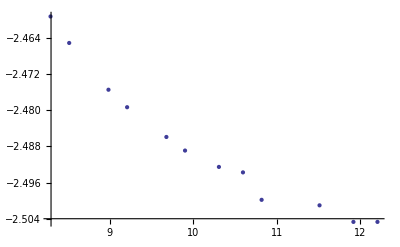

```mathematica
x=Maxx[[All,1]];
y=Maxx[[All,2]];
dat=Table[{Log[x[[i]]],Log[y[[i]]]},{i,1,Length[x]}];
pic1=ListPlot[dat]
```

```mathematica
dat
```

{{Log[4000],-2.45924},{Log[5000],-2.4651},{Log[8000],-2.47545},{Log[10000],-2.47932},{Log[16000],-2.48591},{Log[20000],-2.48891},{Log[30000],-2.49254},{Log[40000],-2.49375},{Log[50000],-2.49982},{Log[100000],-2.50104},{Log[150000],-2.5047},{Log[200000],-2.5047}}

```mathematica
ClearAll[x]
```

(1424.26 fit :)/x^0.5

0.998601 = r0

0.5 = α0

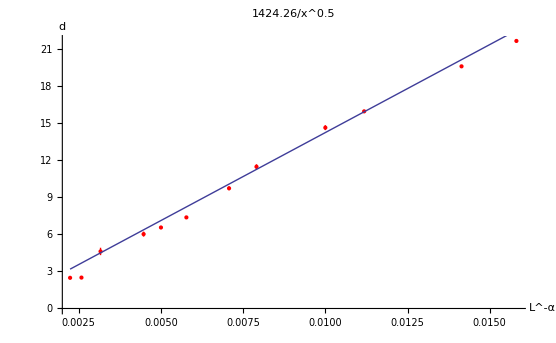

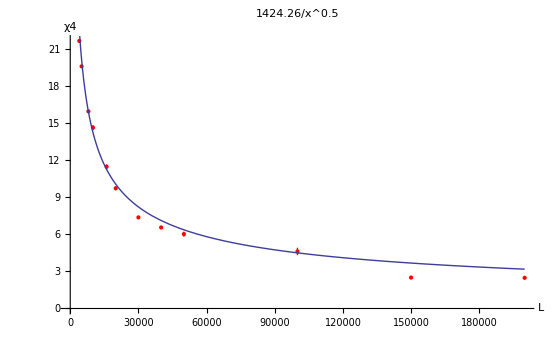

{1424.26/x^0.5, | Estimate | Standard Error | t-Statistic | P-Value
k | 1424.26 | 16.0738 | 88.6076 | 4.71824×10^-17}

FittedModel[8.03351-0.588713 x]

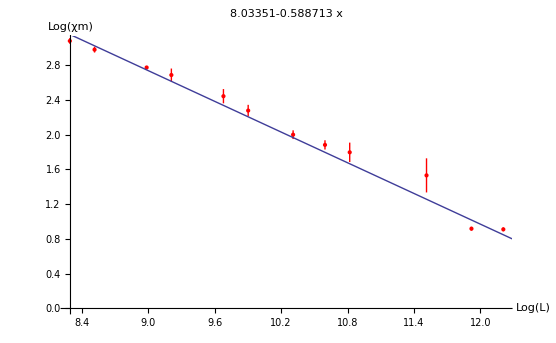

{8.03351-0.588713 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 8.03351 | 0.143507 | 55.9799 | 8.02493×10^-14
x | -0.588713 | 0.0138211 | -42.5953 | 1.22053×10^-12}

```mathematica
r0=0;
For[α=0.0,α<1,α+=0.01;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
model=k*x^-α;
fit=NonlinearModelFit[Maxys,model,{k},x,Weights->1/Errorx^2];

r=fit["RSquared"];
If[r>r0,
ffit=fit["BestFit"];
val=fit["ParameterTableEntries"];
r0=r;
α0=α;
fitf=fit;
]


]
ffit "fit : "
r0 "= r0"
α0 "= α0"
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
erry=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
maxyerrs=Table[{Maxys[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxyerrs,PlotStyle->Red,AxesLabel->{"L^-α","d"},PlotLabel->ffit];

(*pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];*)
pic2=Plot[val[[1]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
pic1=ErrorListPlot[maxyerr,PlotStyle->Red,AxesLabel->{"L","χ4"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]*x^-α0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]



ClearAll[k,x,z]
Maxyαcheck=Table[{Log[Maxy[[All,1]][[i]]],Log[Maxy[[All,2]][[i]]]},{i,1,Length[Maxy]}];
Erroryαcheck=Table[Errory[[i]]/Maxyαcheck[[All,2]][[i]],{i,1,Length[Maxy]}];
model=k-z*x;
fit=LinearModelFit[Maxyαcheck,{1,x},x,Weights->1/Erroryαcheck^2]

maxvαcheckerr=Table[{Maxyαcheck[[i]],ErrorBar[Erroryαcheck[[i]]]},{i,0,Length[Erroryαcheck]}];
ffit=fit["BestFit"];
fitf=fit;
val=fit["ParameterTableEntries"];
pic1=ErrorListPlot[maxvαcheckerr,PlotRange->Full,PlotStyle->Red,AxesLabel->{"Log(L)","Log(χm)"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,7,13},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

fit :  (-4.90087+531.955/x^0.36)

0.992148 = r0

0.36 = α0

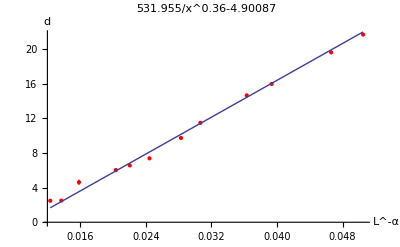

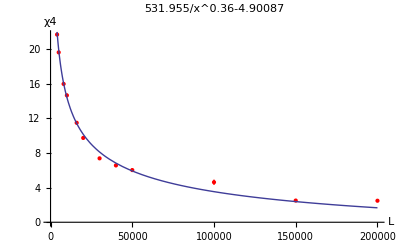

{-4.90087+531.955/x^0.36, | Estimate | Standard Error | t-Statistic | P-Value
1 | -4.90087 | 0.530758 | -9.23372 | 3.28423×10^-6
1/x^0.36 | 531.955 | 14.9647 | 35.5472 | 7.36802×10^-12}

```mathematica
ClearAll[z,r,x]
r0=0;
For[α=0.0,α<1,α+=0.01;
Maxys=Table[{Maxy[[All,1]][[i]],Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
model=k*x^-α;
fit=LinearModelFit[Maxys,{1,x^-α},x,Weights->1/Errorx^2];

r=fit["RSquared"];
If[r>r0,
ffit=fit["BestFit"];
val=fit["ParameterTableEntries"];
r0=r;
α0=α;
fitf=fit;
]


]
ffit "fit : "
r0 "= r0"
α0 "= α0"
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
erry=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
maxyerrs=Table[{Maxys[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];

(*pic1=ListPlot[Maxxs,PlotStyle->Red,AxesLabel->{"L^-z","d"},PlotLabel->ffit];*)
pic1=ErrorListPlot[maxyerrs,PlotStyle->Red,AxesLabel->{"L^-α","d"},PlotLabel->ffit];

(*pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];*)
pic2=Plot[val[[1]][[1]]+val[[2]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
Show[{pic1,pic2}]
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
pic1=ErrorListPlot[maxyerr,PlotStyle->Red,AxesLabel->{"L","χ4"},PlotLabel->ffit];
pic3=Plot[val[[1]][[1]]+val[[2]][[1]]*x^-α0,{x,4000,200000},PlotRange->Full];
Show[{pic1,pic3}]
fitf[{"BestFit","ParameterTable"}]
```

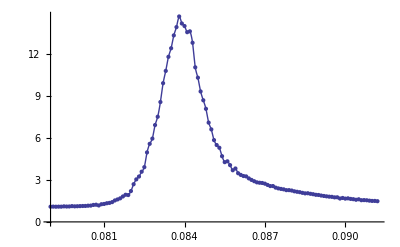

```mathematica
v=9;
l=10;
pic1=ListPlot[Chi[v][l],PlotRange->Full];
pic2=Plot[i4[v][l][x],{x,Chi[v][l][[All,1]][[1]],Chi[v][l][[All,1]][[Length[Chi[v][l]]]]},PlotRange->Full];
Show[{pic1,pic2}]
```

```mathematica
l=10;
Do[
z=0.51;
d0=0.081;
α=0.52;
scale[l]=Table[{(Chi[v][l][[All,1]][[i]]-d0)*((l*1000.)^z),Log[Chi[v][l][[All,2]][[i]]]+α*Log[l*1000.]},{i,1,Length[Chi[v][l]]}];
,{l,{4,5,8,10,16,20,30,40,50,100,150,200}}]
```

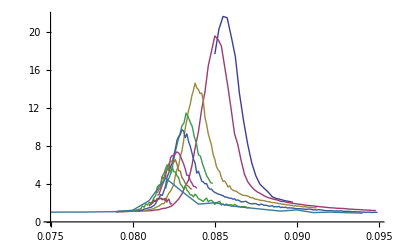

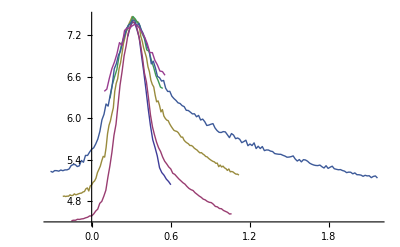

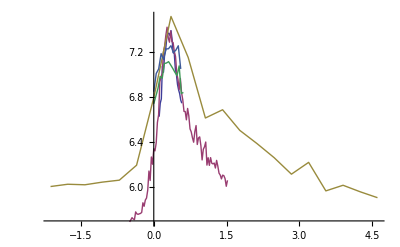

```mathematica
ListLinePlot[{Chi[v][4],Chi[v][5],Chi[v][10],Chi[v][16],Chi[v][20],Chi[v][30],Chi[v][40],Chi[v][50],Chi[v][100],Chi[v][150],Chi[v][200]},PlotRange->Full]
ListLinePlot[{scale[4],scale[5],scale[10],scale[16],scale[20],scale[30]},PlotRange->Full]
ListLinePlot[{scale[40],scale[50],scale[100],scale[150],scale[200]},PlotRange->Full]
```

```mathematica
Maxd[9][100]
```

{{0.082,4.61853},{0.0825,4.04458},{0.0815,3.97664},{0.083,3.20819},{0.0835,2.24727},{0.081,2.24466},{0.085,2.01591},{0.0845,1.92668},{0.084,1.87353},{0.0855,1.83983},{0.086,1.67808},{0.0875,1.63449},{0.0805,1.58105},{0.0865,1.5473},{0.087,1.4924},{0.088,1.31607},{0.0885,1.29558},{0.09,1.26303},{0.0895,1.25915},{0.08,1.2314},{0.0795,1.18312},{0.089,1.1372},{0.0785,1.08325},{0.079,1.07834},{0.078,1.05944},{0.0905,1.05777},{0.0775,1.04803},{0.0765,1.04045},{0.076,1.03987},{0.077,1.03502},{0.092,1.03051},{0.0755,1.02597},{0.075,1.01905},{0.0925,1.00903},{0.091,0.980276},{0.093,0.972311},{0.0935,0.946607},{0.0915,0.930128},{0.094,0.922815},{0.0945,0.870434}}

```mathematica
errorx[150]=0.0003
errory[150]=0.02
```

0.0003

0.02

```mathematica
errorx[100]
```

0.00025

```mathematica
Errorx={errorx[4],errorx[5],errorx[8],errorx[10],errorx[16],errorx[20],errorx[30],errorx[40],errorx[50],errorx[100],errorx[150],errorx[200]}
Errory={errory[4],errory[5],errory[8],errory[10],errory[16],errory[20],errory[30],errory[40],errory[50],errory[100],errory[150],errory[200]}
```

{0.00025,0.0001,0.00025,0.00005,0.00025,0.0002,0.0001,0.0003,0.0003,0.00025,0.0003,0.0003}

{0.1,0.1,0.05,0.2,0.2,0.15,0.1,0.1,0.2,0.3,0.02,0.02}

```mathematica
maxx=Table[{dataoptb01[[i]],ErrorBar[errors1[[i]]]},{i,0,Length[dataoptb01]}];
```

```mathematica
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}];
errx=Table[Errory[[i]]*(-α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}];
pic1=ListPlot[Maxys,PlotStyle->Red,AxesLabel->{"L^-α","χ4"},PlotLabel->ffit];
pic2=Plot[val[[1]][[1]]*x,{x,Maxy[[All,1]][[1]]^-α0,Maxy[[All,1]][[Length[Maxx]]]^-α0}];
```

```mathematica
Maxys=Table[{Maxy[[All,1]][[i]]^-α0,Maxy[[All,2]][[i]]},{i,1,Length[Maxy]}]
errx=Table[Errory[[i]]*(α0)*Maxy[[All,1]][[i]]^(-α0-1),{i,1,Length[Errory]}]
```

{{0.0133946,21.6589},{0.0119271,19.6032},{0.009341,15.9592},{0.00831764,14.6401},{0.00651415,11.4767},{0.00580049,9.72939},{0.00469783,7.37444},{0.0040451,6.55731},{0.00360193,6.02102},{0.00251189,4.61853},{0.00203438,2.50289},{0.00175172,2.48373}}

{1.74129×10^-7,1.24042×10^-7,3.03582×10^-8,8.65034×10^-8,4.2342×10^-8,2.26219×10^-8,8.1429×10^-9,5.25862×10^-9,7.49202×10^-9,3.91854×10^-9,1.4105×10^-10,9.10894×10^-11}

```mathematica
Maxy
```

{{4000,21.6589},{5000,19.6032},{8000,15.9592},{10000,14.6401},{16000,11.4767},{20000,9.72939},{30000,7.37444},{40000,6.55731},{50000,6.02102},{100000,4.61853},{150000,2.50289},{200000,2.48373}}

```mathematica
maxyerr=Table[{Maxy[[i]],ErrorBar[Errory[[i]]]},{i,0,Length[Errory]}];
maxxerr=Table[{Maxx[[i]],ErrorBar[Errorx[[i]]]},{i,0,Length[Errorx]}];
ErrorListPlot[maxxerr,PlotRange->Full]
ErrorListPlot[maxyerr]
```

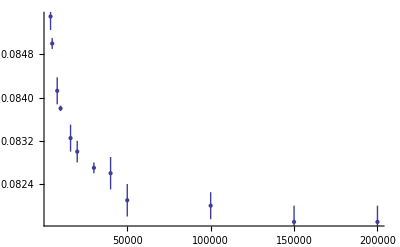

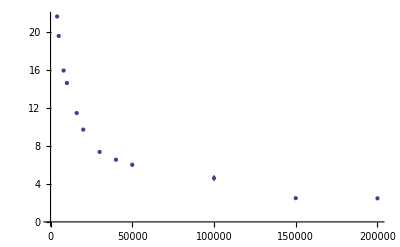

```mathematica
ErrorListPlot[maxxerr,PlotRange->Full]
ErrorListPlot[maxyerr]
```

```mathematica
-----
```

```mathematica
Chi[9][4] 
Chi[9][5] 
Chi[9][8]  
Chi[9][10] 
Chi[9][20] 
Chi[9][30] 
Chi[9][40]
Chi[9][50]
Chi[9][100]
Chi[9][150]
Chi[9][200]
```

{{0.085,17.6917},{0.08525,20.3196},{0.0855,21.6589},{0.08575,21.5283},{0.086,19.5392},{0.08625,17.4133},{0.0865,13.5228},{0.08675,10.6591},{0.087,8.19182},{0.08725,6.2005},{0.0875,4.846},{0.08775,3.96213},{0.088,3.54686},{0.08825,3.13637},{0.0885,2.64321},{0.08875,2.46219},{0.089,2.36908},{0.08925,2.24017},{0.0895,2.16395},{0.08975,2.06394}}

{{0.079,1.09112},{0.0791,1.09112},{0.0792,1.09982},{0.0793,1.09982},{0.0794,1.09934},{0.0795,1.09934},{0.0796,1.11536},{0.0797,1.11441},{0.0798,1.11285},{0.0799,1.11285},{0.08,1.12031},{0.0801,1.12081},{0.0802,1.12508},{0.0803,1.12508},{0.0804,1.13871},{0.0805,1.13871},{0.0806,1.14854},{0.0807,1.14854},{0.0808,1.17044},{0.0809,1.17044},{0.081,1.16726},{0.0811,1.17276},{0.0812,1.20792},{0.0813,1.20078},{0.0814,1.2427},{0.0815,1.26914},{0.0816,1.28094},{0.0817,1.30276},{0.0818,1.42067},{0.0819,1.38828},{0.082,1.42999},{0.0821,1.46055},{0.0822,1.56254},{0.0823,1.55203},{0.0824,1.66834},{0.0825,1.7265},{0.0826,1.99193},{0.0827,2.10247},{0.0828,2.42464},{0.0829,2.40837},{0.083,2.96909},{0.0831,2.92233},{0.0832,3.59575},{0.0833,3.91496},{0.0834,4.34891},{0.0835,4.47086},{0.0836,5.96186},{0.0837,5.76338},{0.0838,7.63238},{0.0839,7.9277},{0.084,9.6833},{0.0841,9.25778},{0.0842,11.4545},{0.0843,12.2976},{0.0844,13.7536},{0.0845,13.6769},{0.0846,16.4799},{0.0847,16.3906},{0.0848,18.4033},{0.0849,17.6357},{0.085,19.8527},{0.0851,19.3536},{0.0852,18.9617},{0.0853,19.493},{0.0854,18.5983},{0.0855,18.4627},{0.0856,16.5381},{0.0857,16.1771},{0.0858,13.9546},{0.0859,14.4813},{0.086,11.6952},{0.0861,11.8901},{0.0862,9.14305},{0.0863,9.46211},{0.0864,8.14679},{0.0865,8.13284},{0.0866,6.77131},{0.0867,6.19926},{0.0868,5.05354},{0.0869,5.05228},{0.087,4.30025},{0.0871,4.19},{0.0872,3.92389},{0.0873,3.63034},{0.0874,3.33132},{0.0875,3.47635},{0.0876,3.12613},{0.0877,3.15693},{0.0878,2.90131},{0.0879,3.04179},{0.088,2.74514},{0.0881,2.74902},{0.0882,2.59524},{0.0883,2.57369},{0.0884,2.50492},{0.0885,2.46729},{0.0886,2.39224},{0.0887,2.36686},{0.0888,2.33464},{0.0889,2.28855},{0.089,2.15138},{0.0891,2.191},{0.0892,2.13132},{0.0893,2.13914},{0.0894,2.03851},{0.0895,2.09102},{0.0896,1.96285},{0.0897,2.03646},{0.0898,1.95281},{0.0899,1.93998},{0.09,1.87527},{0.0901,1.91121},{0.0902,1.83714},{0.0903,1.87352},{0.0904,1.80844},{0.0905,1.77715},{0.0906,1.72722},{0.0907,1.75852},{0.0908,1.68817},{0.0909,1.73503},{0.091,1.69038},{0.0911,1.69218},{0.0912,1.61288},{0.0913,1.662},{0.0914,1.60244},{0.0915,1.5981},{0.0916,1.55189},{0.0917,1.57262},{0.0918,1.5238},{0.0919,1.54237},{0.092,1.50973},{0.0921,1.47697},{0.0922,1.48114},{0.0923,1.47253},{0.0924,1.45319},{0.0925,1.43611},{0.0926,1.4303},{0.0927,1.42178},{0.0928,1.42352},{0.0929,1.41497},{0.093,1.39445},{0.0931,1.37847},{0.0932,1.34952},{0.0933,1.33662},{0.0934,1.33857},{0.0935,1.33089},{0.0936,1.29027},{0.0937,1.31645},{0.0938,1.29502},{0.0939,1.30324},{0.094,1.26406},{0.0941,1.26998},{0.0942,1.24872},{0.0943,1.25105},{0.0944,1.22692},{0.0945,1.23937},{0.0946,1.19732},{0.0947,1.2091},{0.0948,1.20738},{0.0949,1.2076}}

{{0.083,5.59573},{0.083125,6.68262},{0.08325,8.03144},{0.083375,9.38686},{0.0835,10.7669},{0.083625,12.2905},{0.08375,13.0896},{0.083875,14.417},{0.084,15.5326},{0.084125,15.9592},{0.08425,15.7909},{0.084375,15.8505},{0.0845,15.4406},{0.084625,13.964},{0.08475,13.0325},{0.084875,11.8188},{0.085,10.5661},{0.085125,9.26867},{0.08525,8.12474},{0.085375,6.87957},{0.0855,6.48408},{0.085625,5.72621},{0.08575,5.16224},{0.085875,4.78831}}

{{0.079,1.08213},{0.0791,1.08934},{0.0792,1.08268},{0.0793,1.08711},{0.0794,1.0862},{0.0795,1.10469},{0.0796,1.09635},{0.0797,1.09994},{0.0798,1.12756},{0.0799,1.10504},{0.08,1.11129},{0.0801,1.12322},{0.0802,1.13389},{0.0803,1.1338},{0.0804,1.14384},{0.0805,1.16569},{0.0806,1.21667},{0.0807,1.23263},{0.0808,1.171},{0.0809,1.26918},{0.081,1.29385},{0.0811,1.33209},{0.0812,1.34147},{0.0813,1.42033},{0.0814,1.53504},{0.0815,1.57889},{0.0816,1.70739},{0.0817,1.77078},{0.0818,1.93924},{0.0819,1.92443},{0.082,2.2095},{0.0821,2.75139},{0.0822,3.05424},{0.0823,3.16928},{0.0824,3.53123},{0.0825,3.97647},{0.0826,4.91985},{0.0827,5.39909},{0.0828,6.05269},{0.0829,7.04351},{0.083,7.35173},{0.0831,8.51448},{0.0832,9.80122},{0.0833,10.729},{0.0834,11.8145},{0.0835,12.5349},{0.0836,13.2429},{0.0837,13.9095},{0.0838,14.6984},{0.0839,14.3486},{0.084,13.8776},{0.0841,13.5142},{0.0842,13.692},{0.0843,12.8356},{0.0844,11.0594},{0.0845,10.3944},{0.0846,9.3269},{0.0847,8.5547},{0.0848,8.12564},{0.0849,6.96692},{0.085,6.54902},{0.0851,5.96719},{0.0852,5.55898},{0.0853,5.23291},{0.0854,4.70127},{0.0855,4.24428},{0.0856,4.26677},{0.0857,4.08177},{0.0858,3.71467},{0.0859,3.7466},{0.086,3.4764},{0.0861,3.36264},{0.0862,3.20988},{0.0863,3.25203},{0.0864,3.102},{0.0865,2.98843},{0.0866,2.88725},{0.0867,2.82387},{0.0868,2.7828},{0.0869,2.78326},{0.087,2.7071},{0.0871,2.63764},{0.0872,2.54969},{0.0873,2.55587},{0.0874,2.42994},{0.0875,2.39484},{0.0876,2.3555},{0.0877,2.31075},{0.0878,2.27753},{0.0879,2.25695},{0.088,2.24972},{0.0881,2.18829},{0.0882,2.1545},{0.0883,2.11932},{0.0884,2.07902},{0.0885,2.04277},{0.0886,2.04362},{0.0887,1.99902},{0.0888,1.97625},{0.0889,1.94403},{0.089,1.92885},{0.0891,1.86784},{0.0892,1.84187},{0.0893,1.82265},{0.0894,1.80967},{0.0895,1.77408},{0.0896,1.73413},{0.0897,1.76151},{0.0898,1.66116},{0.0899,1.70873},{0.09,1.67156},{0.0901,1.68122},{0.0902,1.63882},{0.0903,1.62157},{0.0904,1.58742},{0.0905,1.60912},{0.0906,1.5406},{0.0907,1.56054},{0.0908,1.54081},{0.0909,1.49858},{0.091,1.50397},{0.0911,1.50184},{0.0912,1.47665},{0.0913,1.43674},{0.0914,1.47413},{0.0915,1.42955},{0.0916,1.44547},{0.0917,1.41913},{0.0918,1.41791},{0.0919,1.38476},{0.092,1.38896},{0.0921,1.35838},{0.0922,1.35894},{0.0923,1.33986},{0.0924,1.31553},{0.0925,1.32344},{0.0926,1.31758},{0.0927,1.29201},{0.0928,1.28985},{0.0929,1.30111},{0.093,1.286},{0.0931,1.27052},{0.0932,1.23181},{0.0933,1.24388},{0.0934,1.23121},{0.0935,1.23194},{0.0936,1.20318},{0.0937,1.20433},{0.0938,1.1848},{0.0939,1.17652},{0.094,1.19035},{0.0941,1.15792},{0.0942,1.14512},{0.0943,1.15678},{0.0944,1.12413},{0.0945,1.13359},{0.0946,1.11001},{0.0947,1.10569},{0.0948,1.10899},{0.0949,1.12592}}

{{0.079,1.08419},{0.0791,1.07194},{0.0792,1.10031},{0.0793,1.09905},{0.0794,1.08744},{0.0795,1.1087},{0.0796,1.09643},{0.0797,1.11076},{0.0798,1.11225},{0.0799,1.12535},{0.08,1.1881},{0.0801,1.20243},{0.0802,1.20847},{0.0803,1.17017},{0.0804,1.17244},{0.0805,1.26063},{0.0806,1.22998},{0.0807,1.3774},{0.0808,1.37357},{0.0809,1.41713},{0.081,1.51471},{0.0811,1.51294},{0.0812,1.56018},{0.0813,1.73737},{0.0814,1.91959},{0.0815,2.23563},{0.0816,2.49316},{0.0817,2.91365},{0.0818,2.76017},{0.0819,3.16096},{0.082,3.81444},{0.0821,4.85596},{0.0822,5.25763},{0.0823,5.77517},{0.0824,6.1561},{0.0825,7.00013},{0.0826,7.72812},{0.0827,8.50455},{0.0828,9.03449},{0.0829,9.17585},{0.083,9.62399},{0.0831,9.74574},{0.0832,8.86044},{0.0833,9.52576},{0.0834,8.58065},{0.0835,8.00505},{0.0836,7.12709},{0.0837,6.65544},{0.0838,6.29666},{0.0839,5.12431},{0.084,5.23765},{0.0841,4.9203},{0.0842,4.3275},{0.0843,4.07949},{0.0844,4.04219},{0.0845,4.1048},{0.0846,3.62871},{0.0847,3.47251},{0.0848,3.42571},{0.0849,3.23237},{0.085,3.10424},{0.0851,3.03272},{0.0852,2.9308},{0.0853,2.89702},{0.0854,2.84267},{0.0855,2.76493},{0.0856,2.61894},{0.0857,2.61249},{0.0858,2.55878},{0.0859,2.48468},{0.086,2.50201},{0.0861,2.41988},{0.0862,2.4872},{0.0863,2.28899},{0.0864,2.30983},{0.0865,2.23499},{0.0866,2.12184},{0.0867,2.14267},{0.0868,2.13231},{0.0869,2.18744},{0.087,2.04564},{0.0871,1.97757},{0.0872,1.91021},{0.0873,1.92444},{0.0874,1.92708},{0.0875,1.95857},{0.0876,1.84514},{0.0877,1.7776},{0.0878,1.84875},{0.0879,1.83814},{0.088,1.73688},{0.0881,1.73442},{0.0882,1.7199},{0.0883,1.64677},{0.0884,1.66585},{0.0885,1.70566},{0.0886,1.57364},{0.0887,1.61107},{0.0888,1.59246},{0.0889,1.63891},{0.089,1.51667},{0.0891,1.55859},{0.0892,1.49688},{0.0893,1.54831},{0.0894,1.46984},{0.0895,1.4867},{0.0896,1.46805},{0.0897,1.46513},{0.0898,1.44805},{0.0899,1.41385},{0.09,1.39826},{0.0901,1.39095},{0.0902,1.40325},{0.0903,1.35597},{0.0904,1.34908},{0.0905,1.32155},{0.0906,1.33004},{0.0907,1.33242},{0.0908,1.37331},{0.0909,1.29431},{0.091,1.25473},{0.0911,1.28647},{0.0912,1.2631},{0.0913,1.28618},{0.0914,1.28218},{0.0915,1.25926},{0.0916,1.21148},{0.0917,1.21834},{0.0918,1.18261},{0.0919,1.19261},{0.092,1.18806},{0.0921,1.20493},{0.0922,1.16572},{0.0923,1.14373},{0.0924,1.16568},{0.0925,1.13044},{0.0926,1.15559},{0.0927,1.15194},{0.0928,1.13033},{0.0929,1.11975},{0.093,1.11449},{0.0931,1.11279},{0.0932,1.11951},{0.0933,1.0925},{0.0934,1.06476},{0.0935,1.07041},{0.0936,1.07623},{0.0937,1.05182},{0.0938,1.06238},{0.0939,1.03386},{0.094,1.03522},{0.0941,1.02277},{0.0942,1.00867},{0.0943,1.02404},{0.0944,1.02906},{0.0945,1.02868},{0.0946,1.00126},{0.0947,1.00073},{0.0948,1.01595},{0.0949,0.990308}}

{{0.0815,2.78726},{0.0816,2.90381},{0.0817,3.34819},{0.0818,3.8502},{0.0819,4.40051},{0.082,4.78041},{0.0821,5.66584},{0.0822,5.41899},{0.0823,6.77538},{0.0824,6.8202},{0.0825,7.00093},{0.0826,7.28042},{0.0827,7.3273},{0.0828,7.09106},{0.0829,6.85999},{0.083,6.65678},{0.0831,6.20046},{0.0832,5.52392},{0.0833,4.98197},{0.0834,4.91202},{0.0835,4.28834},{0.0836,4.12661},{0.0837,3.75155},{0.0838,3.77792},{0.0839,3.48901}}

{{0.0815,3.11905},{0.0816,3.51787},{0.0817,3.57145},{0.0818,4.63823},{0.0819,4.55384},{0.082,5.42887},{0.0821,5.60981},{0.0822,6.2603},{0.0823,6.28262},{0.0824,6.51051},{0.0825,6.33484},{0.0826,6.46595},{0.0827,6.00119},{0.0828,5.47066},{0.0829,5.37113},{0.083,4.76706},{0.0831,4.40959},{0.0832,4.14214},{0.0833,3.80288},{0.0834,3.68699},{0.0835,3.52009},{0.0836,3.35348},{0.0837,3.07166},{0.0838,3.03231},{0.0839,2.9355}}

{{0.079,1.07059},{0.0791,1.08689},{0.0792,1.11198},{0.0793,1.09592},{0.0794,1.08866},{0.0795,1.17383},{0.0796,1.15445},{0.0797,1.14335},{0.0798,1.15299},{0.0799,1.15743},{0.08,1.14602},{0.0801,1.27228},{0.0802,1.22132},{0.0803,1.30779},{0.0804,1.32097},{0.0805,1.43945},{0.0806,1.58585},{0.0807,1.56137},{0.0808,1.83952},{0.0809,1.81221},{0.081,2.11255},{0.0811,1.98058},{0.0812,2.08516},{0.0813,2.59487},{0.0814,2.83065},{0.0815,3.65272},{0.0816,3.89305},{0.0817,4.07138},{0.0818,4.69648},{0.0819,5.10833},{0.082,5.63922},{0.0821,6.11417},{0.0822,5.58984},{0.0823,5.23476},{0.0824,5.97086},{0.0825,5.212},{0.0826,5.26564},{0.0827,4.87382},{0.0828,4.42178},{0.0829,4.00388},{0.083,3.78762},{0.0831,3.38344},{0.0832,3.70064},{0.0833,3.26697},{0.0834,3.06719},{0.0835,2.87755},{0.0836,2.85482},{0.0837,2.66896},{0.0838,2.8756},{0.0839,2.74484},{0.084,2.44303},{0.0841,2.39668},{0.0842,2.24942},{0.0843,2.13787},{0.0844,2.3615},{0.0845,2.48726},{0.0846,2.14977},{0.0847,2.28683},{0.0848,2.21984},{0.0849,2.16654},{0.085,1.89208},{0.0851,2.01775},{0.0852,2.03043},{0.0853,2.16704},{0.0854,1.77311},{0.0855,1.93532},{0.0856,1.78682},{0.0857,1.89252},{0.0858,1.79342},{0.0859,1.75184},{0.086,1.82046},{0.0861,1.76762},{0.0862,1.84086},{0.0863,1.74001},{0.0864,1.64309},{0.0865,1.62494},{0.0866,1.56409},{0.0867,1.63254},{0.0868,1.59073},{0.0869,1.57804},{0.087,1.50747},{0.0871,1.56716}}

Chi[9][100]

{{0.081,1.72209},{0.0811,1.84439},{0.0812,1.977},{0.0813,2.19503},{0.0814,2.16116},{0.0815,2.46309},{0.0816,2.47341},{0.0817,2.50289},{0.0818,2.42979},{0.0819,2.3551},{0.082,2.27551},{0.0821,2.21261},{0.0822,2.41099},{0.0823,1.88847},{0.0824,1.90328}}

{{0.081,1.65062},{0.0811,1.93998},{0.0812,2.021},{0.0813,2.31431},{0.0814,2.19627},{0.0815,2.41275},{0.0816,2.41753},{0.0817,2.48373},{0.0818,2.33552},{0.0819,2.38683},{0.082,2.48237},{0.0821,2.02058}}